```mathematica
(* Analysis specific to AMS-02 *)
```

```mathematica
(* AMS-02 bin data *)
```

```mathematica
amsE={(10.73+11.54)/2,(11.54+12.39)/2,(12.39+13.27)/2,(13.27+14.19)/2,(14.19+15.15)/2,(15.15+16.15)/2,(16.15+17.18)/2,(17.18+18.25)/2,(18.25+19.37)/2,(19.37+20.54)/2,(20.54+21.76)/2,(21.76+23.07)/2,(23.07+24.45)/2,(24.45+25.87)/2,(25.87+27.34)/2,(27.34+28.87)/2,(28.87+30.45)/2,(30.45+32.10)/2,(32.10+33.80)/2,(33.80+35.57)/2,(35.57+37.40)/2,(37.40+40.00)/2,(40.00+43.39)/2,(43.39+47.01)/2,(47.01+50.87)/2,(50.87+54.98)/2,(54.98+59.36)/2,(59.36+64.03)/2,(64.03+69.00)/2,(69.00+74.30)/2,(74.30+80.00)/2,(80.00+86.00)/2,(86.00+92.50)/2,(92.50+100.0)/2,(100.0+115.1)/2,(115.1+132.1)/2,(132.1+151.5)/2,
(151.5+173.5)/2,(173.5+206.0)/2,(206.0+260.0)/2,(260.0+350.0)/2,(350.0+500.0)/2};
```

```mathematica
poscounts={9504,7846,7646,6457,5704,5419,4689,4016,3906,3777,3244,2910,2813,2631,2397,2325,2040,1706,1530,1496,1327,1607,1616,1401,1116,1041,837,710,644,606,450,381,398,358,524,365,271,228,225,178,135,72};
```

```mathematica
posfrac={0.0532,0.0546,0.0553,0.0552,0.0558,0.0570,0.0585,0.0601,0.0596,0.0625,0.0617,0.0640,0.0655,0.0652,0.0662,0.0704,0.0717,0.0719,0.0721,0.0766,0.0732,0.0781,0.0806,0.0872,0.0840,0.0887,0.0921,0.0933,0.0974,0.1069,0.0963,0.1034,0.1207,0.1169,0.1205,0.1110,0.1327,0.1374,0.1521,0.1550,0.1590,0.1471};
```

```mathematica
totalcounts=poscounts/posfrac;
```

```mathematica
(**** Run MC for each AMS-02 high-energy bin midpoint and save angle data. ****)
```

```mathematica
samples=100;
```

```mathematica
anglesamples=Map[{#1,angleMC[#1,samples]}&,amsE];
```

```mathematica
(*** Plot the results ***)
```

```mathematica
avgangles=Map[Mean[#[[2]][[All,3]]]&,anglesamples];
```

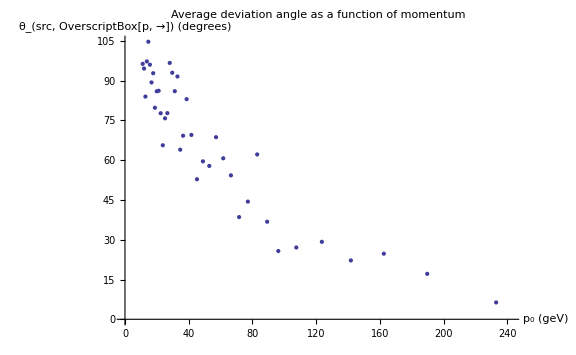

```mathematica
ListPlot[Transpose[{amsE,avgangles*180/π}],PlotLabel->"Average deviation angle as a function of observed momentum",AxesLabel->{"p_0 (geV)","θ_(src, OverscriptBox[p, →]) (degrees)"},ImageSize->Large]
```

```mathematica
(* Other plotting tools *)
```

```mathematica
DensityHistogram[Drop[mcangles,{},{2}]*180/π,PlotLabel->"Angle between observed momentum and source (p="<>ToString[p0]<>" GeV)",AxesLabel->{"θ_obs (degrees)","θ_(src, OverscriptBox[p, →]) (degrees)"},ColorFunction->"SolarColors",ChartLegends->Placed[Automatic,Right]]
```

```mathematica
DensityHistogram[Drop[mcangles,{},{1}]*180/π,PlotLabel->"Angle between observed momentum and source (p=100 GeV)",AxesLabel->{"ϕ_obs (degrees)","θ_(src, OverscriptBox[p, →]) (degrees)"},ColorFunction->"SolarColors",ChartLegends->Placed[Automatic,Right]]
```

```mathematica
Histogram[mcangles[[All,3]]*180/π,AxesLabel->{"θ_(src, OverscriptBox[p, →]) (degrees)"},PlotLabel->"Angle between observed momentum and source (p=100 GeV)"]
```